```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/thermodynamic_integration_analysis/GibbsBog/nov16_x_free_4_longRun_4.8_4_3_v1v2_noholdcutoffs/2MEAM_Hessian_run"];
dudlFiles={"LinScaled_T_all_vol_dudl"};
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number,Number}],{i,1,1}];
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11];
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,3}];
ttt={300,760,1900,2500,3200,3800};
vols={4.6583,4.685,4.730,4.759,4.801,4.850};
```

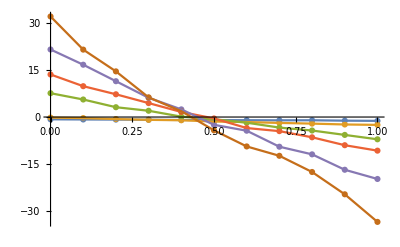

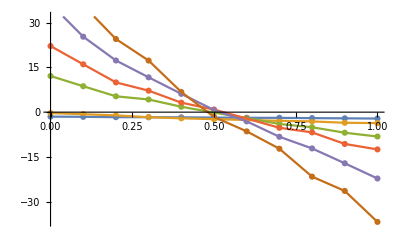

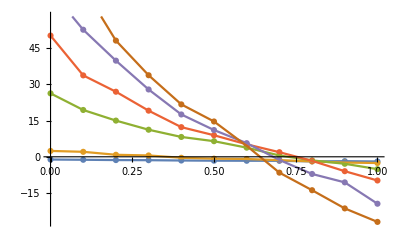

```mathematica
Show[{ListPlot@dudlAll[[1]],ListLinePlot@dudlAll[[1]]}]
Show[{ListPlot@dudlAll[[2]],ListLinePlot@dudlAll[[2]]}]
Show[{ListPlot@dudlAll[[3]],ListLinePlot@dudlAll[[3]]}]
```

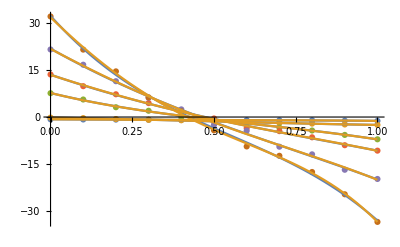

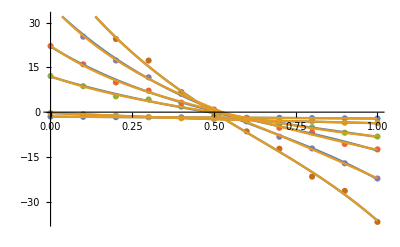

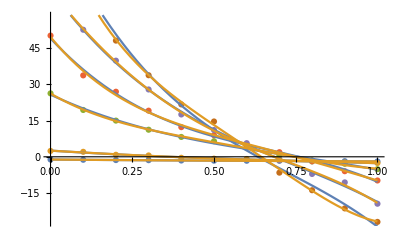

```mathematica
dudlAllFit1=Table[Table[Fit[dudlAll[[vol]][[temp]],{1L,1},L],{temp,1,6,1}],{vol,1,3}];
dudlAllFit2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,3}];
dudlAllFit3=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,3}];
dudlAllFit4=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^4,L^2,L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,3}];
Show[ListPlot[dudlAll[[1]]],Plot[{dudlAllFit3[[1]],dudlAllFit4[[1]]},{L,0,1}]]
Show[ListPlot[dudlAll[[2]]],Plot[{dudlAllFit3[[2]],dudlAllFit4[[2]]},{L,0,1}]]
Show[ListPlot[dudlAll[[3]]],Plot[{dudlAllFit3[[3]],dudlAllFit4[[3]]},{L,0,1}]]
```

```mathematica
bound1=0;bound2=1; 
(*Solver 1 - standard *)
mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
mvtSolverNum[arg_]:=mvtSolver[arg][[1]][[1]][[2]][[1]]
(*Integrator*)
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
(*Solver 2 - midpoint*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
(*Solver 3 - l1 l2 norm CS inpsired solver *)
weightedMVT[fun_,mu_,nu_,midpoint_]:=nu*NMinimize[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,x]
mvtNumWeight[arg_,mu_,nu_,midpoint_]:={mvtSolver[arg][[1]][[1]][[2]][[1]],weightedMVT[arg,mu,nu,midpoint]}
```

```mathematica
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],0.01,1,0.5],{i,1,6}]//TableForm
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],200,1,0.5],{i,1,6}]//TableForm
```

0.463556 | 0.0000124984
x→0.465711
0.499476 | 2.74481×10^-9
x→0.499476
0.47108 | 8.36303×10^-6
x→0.471082
0.467422 | 0.0000106133
x→0.467422
0.474672 | 6.41523×10^-6
x→0.474672
0.466379 | 0.0000113035
x→0.466379

0.463556 | 0.000194063
x→0.499975
0.499476 | 1.80421×10^-6
x→0.499983
0.47108 | 0.0706261
x→0.487832
0.467422 | 0.154309
x→0.476344
0.474672 | 0.113434
x→0.47761
0.466379 | 0.208078
x→0.46906

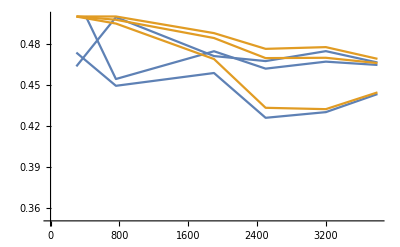

```mathematica
dataMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,3}];
dataWMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,3}];
Show[Table[ListLinePlot[{dataMVT4[[i]],dataWMVT4[[i]]},PlotRange->{{0,3800},{0.35,0.5}}],{i,1,3}]]
```

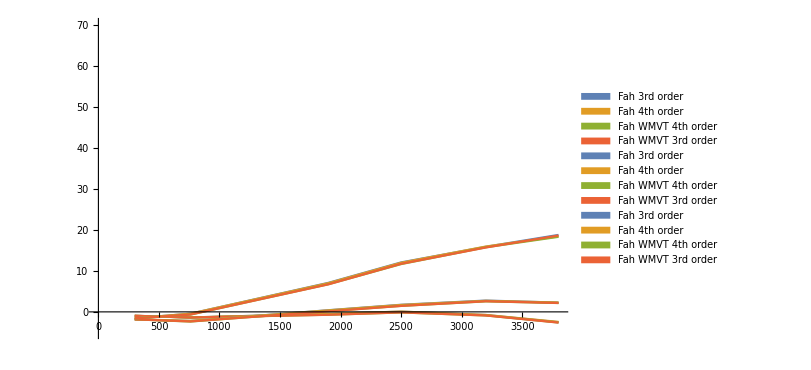

```mathematica
datafahMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,3}];
datafahWMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,3}];
datafahMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,3}];
datafahWMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,3}];
Show[Table[ListLinePlot[{datafahMVT3[[i]],datafahMVT4[[i]],datafahWMVT4[[i]],datafahWMVT3[[i]]},PlotRange->{{0,3800},{-5,70}},PlotLegends->SwatchLegend[{"Fah 3rd order","Fah 4th order","Fah WMVT 4th order","Fah WMVT 3rd order"}]],{i,1,3}],ImageSize->600]
```

```mathematica
Table[Table[mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,3}]//TableForm
Table[Table[mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,3}]//TableForm
```

0.499975 | 0.499983 | 0.487832 | 0.476344 | 0.47761 | 0.46906
0.500023 | 0.497582 | 0.484253 | 0.469584 | 0.469832 | 0.465952
0.499927 | 0.494823 | 0.468917 | 0.433305 | 0.432315 | 0.444554

0.500005 | 0.499903 | 0.486931 | 0.478654 | 0.480296 | 0.478825
0.500007 | 0.498171 | 0.476235 | 0.460167 | 0.461644 | 0.466851
0.499919 | 0.495578 | 0.453021 | 0.4216 | 0.437323 | 0.423372

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/ZrC_analysis/Data/TI/GibbsBog-nov16_x_free_4_longRun_4.8_4_3_v1v2_noholdcutoffs"];
tiRotFiles={"vol_ZrFitTrue_CFitTrue"};
(*Format:  volume ZrFitted ZrTrue CFitted CTrue
*)
tiRotDataRaw=Table[ReadList[tiRotFiles[[i]],{Number, Number,Number,Number,Number}],{i,1,1}][[1]];
tiRotDataRaw
```

{{4.6583,-0.13083,-0.13278,-0.18384,-0.1848},{4.685,-0.12084,-0.1264,-0.1709,-0.17419},{4.73,-0.10344,-0.1161,-0.14892,-0.15725},{4.759,-0.09285,-0.1098,-0.13462,-0.147},{4.801,-0.08735,-0.10111,-0.12361,-0.133},{4.85,-0.08366,-0.09161,-0.11433,-0.11788}}

```mathematica
tiRotData=Table[Transpose[{Transpose[tiRotDataRaw][[1]],Transpose[tiRotDataRaw][[1+i]]}],{i,1,4}]
```

{{{4.6583,-0.13083},{4.685,-0.12084},{4.73,-0.10344},{4.759,-0.09285},{4.801,-0.08735},{4.85,-0.08366}},{{4.6583,-0.13278},{4.685,-0.1264},{4.73,-0.1161},{4.759,-0.1098},{4.801,-0.10111},{4.85,-0.09161}},{{4.6583,-0.18384},{4.685,-0.1709},{4.73,-0.14892},{4.759,-0.13462},{4.801,-0.12361},{4.85,-0.11433}},{{4.6583,-0.1848},{4.685,-0.17419},{4.73,-0.15725},{4.759,-0.147},{4.801,-0.133},{4.85,-0.11788}}}

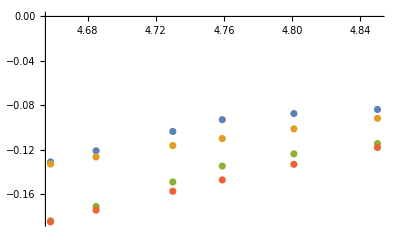

284.571-186.298 x+40.5306 x^2-2.93199 x^3
-6.49901+2.89826 x-0.416483 x^2+0.0188241 x^3
391.854-253.986 x+54.7343 x^2-3.92363 x^3
-19.1849+9.93858 x-1.72754 x^2+0.100811 x^3

```mathematica
ListPlot@tiRotData[[1;;4]]
fits=Table[Fit[tiRotData[[i]],{1,x,x^2,x^3},x],{i,1,4}];
fits//TableForm
```

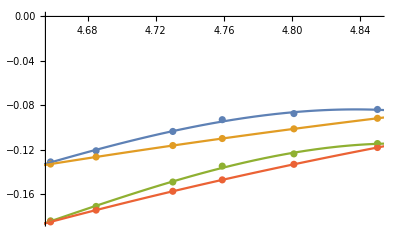

```mathematica
Show[{ListPlot@tiRotData[[1;;4]],Plot[fits,{x,4.6,4.9}]}]
```

#### Average the change in FC, to find new volumes

```mathematica
tiRotDataSum=Table[Transpose[{Transpose[tiRotDataRaw][[1]],Transpose[tiRotDataRaw][[1+i]]+Transpose[tiRotDataRaw][[3+i]]}],{i,1,2,1}]
fitsSum=Table[Fit[tiRotDataSum[[i]],{1,x,x^2,x^3},x],{i,1,2}]
```

{{{4.6583,-0.31467},{4.685,-0.29174},{4.73,-0.25236},{4.759,-0.22747},{4.801,-0.21096},{4.85,-0.19799}},{{4.6583,-0.31758},{4.685,-0.30059},{4.73,-0.27335},{4.759,-0.2568},{4.801,-0.23411},{4.85,-0.20949}}}

{676.425-440.284 x+95.265 x^2-6.85562 x^3,-25.6839+12.8368 x-2.14402 x^2+0.119635 x^3}

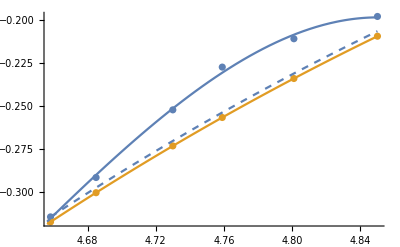

0.00291

```mathematica
Show[{ListPlot@tiRotDataSum,Plot[fitsSum,{x,4.6563,4.850}],Plot[fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]]),{x,4.6583,4.850},PlotStyle->Dashed]}]
```

```mathematica
Table[Solve[fitsSum[[1]]==Evaluate[fitsSum[[2]]/.x->vols[[i]]//N],x][[2]],{i,1,6}]
```

{{x→4.65615},{x→4.67394},{x→4.70375},{x→4.72342},{x→4.7539},{x→4.79881}}

```mathematica
Table[Solve[fitsSum[[2]]==Evaluate[fitsSum[[1]]/.x->vols[[i]]//N],x][[1]],{i,1,6}]
```

{{x→4.6615},{x→4.70173},{x→4.76845},{x→4.80749},{x→4.85182},{x→4.87318}}

0.56385

-2.94125

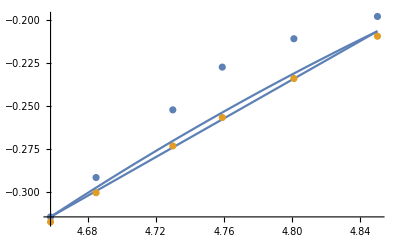

```mathematica
(*c=y1-mx1*)
mDFT=(tiRotDataSum[[2]][[-1]][[2]]-tiRotDataSum[[2]][[1]][[2]])/(tiRotDataSum[[2]][[-1]][[1]]-tiRotDataSum[[2]][[1]][[1]])
cDFT=tiRotDataSum[[1]][[1]][[2]]-mDFT*tiRotDataSum[[1]][[1]][[1]]
FCdft[V_]:=mDFT*V+cDFT
Show[{Plot[Evaluate@FCdft[x],{x,4.6583,4.850},PlotRange->All],ListPlot@tiRotDataSum,Plot[fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]]),{x,4.6583,4.850},PlotRange->All]}]
```

```mathematica
fcDFTnonlinear=fitsSum[[2]]+(tiRotDataSum[[1]][[1]][[2]]-tiRotDataSum[[2]][[1]][[2]])
```

-25.681+12.8368 x-2.14402 x^2+0.119635 x^3

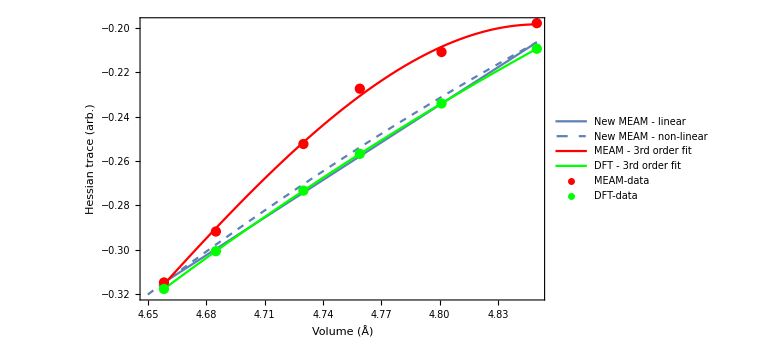

```mathematica
Show[{Plot[FCdft[x],{x,4.6583,4.850},PlotRange->All,PlotLegends->{"New MEAM - linear"},Frame->True,FrameLabel->{"Volume (Å)","Hessian trace (arb.)"},ImageSize->Large],Plot[fcDFTnonlinear,{x,4.65,4.85},PlotStyle->Dashed,PlotLegends->{"New MEAM - non-linear"}],Plot[Evaluate@fitsSum,{x,4.6563,4.850},PlotStyle->{Red,Green},PlotLegends->{"MEAM - 3rd order fit","DFT - 3rd order fit"}],ListPlot[tiRotDataSum,PlotStyle->{Red,Green},PlotLegends->{"MEAM-data","DFT-data"}]}]
```